```mathematica
f[y_,x_,gx_,n_]:= PDF[NormalDistribution[0,1/(√n)],y-gx +x ]
```

```mathematica
g[y_]:=(1-Exp[-2n x (gU - y)] - Exp[2n x (gL - y)] )If[y < gU && y > gL,1,0]
```

```mathematica
FourierTransform[PDF[NormalDistribution[0,1/(√n)],y-gx +x ],y,s,FourierParameters->{0, -2*Pi}]
```

ⅇ^(-(2 π s (ⅈ gx n+π s-ⅈ n x))/n)

```mathematica
FourierTransform[g[y],y,s,FourierParameters->{0, -2*Pi}]
```

1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) (-(ⅇ^(2 gL n x)-ⅇ^(2 gU n x)) n π s x Cos[(gL-gU) π s]+(-ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2) Sin[(gL-gU) π s]) (Cos[(gL+gU) π s]-ⅈ Sin[(gL+gU) π s]) (-1+UnitStep[gL-gU])

```mathematica
ⅇ^(-(2 π s (ⅈ gx n+π s-ⅈ n x))/n)/. s-> t-s
```

ⅇ^(-(2 π (-s+t) (ⅈ gx n+π (-s+t)-ⅈ n x))/n)

```mathematica
1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) (-(ⅇ^(2 gL n x)-ⅇ^(2 gU n x)) n π s x Cos[(gL-gU) π s]+(-ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2) Sin[(gL-gU) π s]) (Cos[(gL+gU) π s]-ⅈ Sin[(gL+gU) π s])/. s-> t
```

(ⅇ^(-2 gU n x) ((-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) n π t x Cos[(gL-gU) π t]+(-ⅇ^(2 gL n x) π^2 t^2+ⅇ^(2 gU n x) n^2 x^2) Sin[(gL-gU) π t]) (Cos[(gL+gU) π t]-ⅈ Sin[(gL+gU) π t]))/(π^3 t^3+n^2 π t x^2)

```mathematica
ghatN[s_,x_,n_,gx_,gU_,gL_]:=NIntegrate[ⅇ^(-(2 π (-s+t) (ⅈ gx n+π (-s+t)-ⅈ n x))/n)*(ⅇ^(-2 gU n x) ((-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) n π t x Cos[(gL-gU) π t]+(-ⅇ^(2 gL n x) π^2 t^2+ⅇ^(2 gU n x) n^2 x^2) Sin[(gL-gU) π t]) (Cos[(gL+gU) π t]-ⅈ Sin[(gL+gU) π t]))/(π^3 t^3+n^2 π t x^2),{t,-∞,∞}]
```

```mathematica
Simplify[1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) (-(ⅇ^(2 gL n x)-ⅇ^(2 gU n x)) n π s x Cos[(gL-gU) π s]+(-ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2) Sin[(gL-gU) π s]) (Cos[(gL+gU) π s]-ⅈ Sin[(gL+gU) π s]) (-1+UnitStep[gL-gU]),gU>gL]
```

-1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) ((-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) n π s x Cos[(gL-gU) π s]+(-ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2) Sin[(gL-gU) π s]) (Cos[(gL+gU) π s]-ⅈ Sin[(gL+gU) π s])

```mathematica
ghat[s_,n_,x_,gL_,gU_]:=-1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) ((-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) n π s x Cos[(gL-gU) π s]+(-ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2) Sin[(gL-gU) π s]) (Cos[(gL+gU) π s]-ⅈ Sin[(gL+gU) π s])
```

```mathematica
ghatb[s_,n_,x_,gL_,gU_]:=1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) (Abs[(-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) n π s x] +Abs[(-ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2)]) If[Abs[s]> 0.001,1,0]+ If[Abs[s]<0.001,(-1+ⅇ^(2 (gL-gU) n x)+(gU-gL)n x)/(n x),0]
```

```mathematica
ghatb2[s_,n_,x_,gL_,gU_]:=1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) (Abs[(-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) s ]n π x +ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2) If[Abs[s]> 0.001,1,0]+ If[Abs[s]<0.001,(-1+ⅇ^(2 (gL-gU) n x)+(gU-gL)n x)/(n x),0]
```

```mathematica
Manipulate[ListLogLogPlot[{Table[Abs[ghat[s,n,x,gL,gU]],{s,1,10}],Table[Abs[ghatN[s,x,n,gx,gU,gL]],{s,1,10}]}],{n,1,10},{gx,0.5,1},{{x,0.5},0,2},{gL,-0.5,-9},{gU, 0.5,3}]
```

```mathematica
Manipulate[LogLogPlot[{Abs[ghat[s,n,x,gL,gU]],Abs[ghatb[s,n,x,gL,gU]],Abs[ghatb2[s,n,x,gL,gU]]},{s,0,10},PlotRange->Full],{n,1,10},{{x,0.5},0,2},{gL,-0.5,-9},{gU, 0.5,3}]
```

```mathematica
Manipulate[LogLogPlot[{Abs[ghat[s,n,x,gL,gU]],Abs[ghatb[s,n,x,gL,gU]],Abs[ghatb2[s,n,x,gL,gU]]},{x,0,10},PlotRange->Full],{n,1,10},{{s,1},1,10},{gL,-0.5,-9},{gU, 0.5,3}]
```

```mathematica
1/(π^3 s^3+n^2 π s x^2)ⅇ^(-2 gU n x) (Abs[(-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) s ]n π x +ⅇ^(2 gL n x) π^2 s^2+ⅇ^(2 gU n x) n^2 x^2) /. s-> t
```

(ⅇ^(-2 gU n x) (ⅇ^(2 gL n x) π^2 t^2+ⅇ^(2 gU n x) n^2 x^2+n π x Abs[(-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) t]))/(π^3 t^3+n^2 π t x^2)

```mathematica
∫_(-∞)^∞ (ⅇ^(-2 gU n x) (ⅇ^(2 gL n x) π^2 t^2+ⅇ^(2 gU n x) n^2 x^2+n π x Abs[(-ⅇ^(2 gL n x)+ⅇ^(2 gU n x)) t]))/(π^3 t^3+n^2 π t x^2)Exp[(-2 π^2 (s-t)^2)/n]ⅆt
```

$Aborted

```mathematica
∫_(-∞)^∞ t/(π^3 t^3+n^2 x^2 π t)Exp[(-2 π^2 (s-t)^2)/n]ⅆt
```

$Aborted

```mathematica
b[s_,n_,x_]:=n π x NIntegrate[t/(π^3 t^3+n^2 x^2 π t)Exp[(-2 π^2 (s-t)^2)/n],{t,-∞,∞}]
```

```mathematica
listb := Table[b[s,5,0.4],{s,1,20}]
```

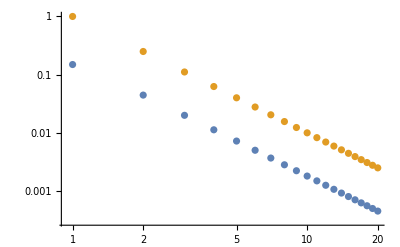

```mathematica
ListLogLogPlot[{listb,Table[1/s^2,{s,1,20}]}]
```

```mathematica
listn := Table[b[4,n,0.4],{n,1,700,50}]
```

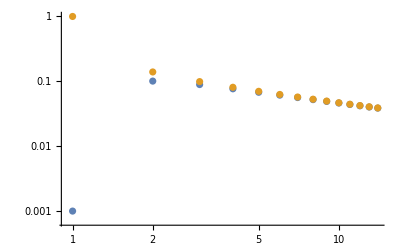

```mathematica
ListLogLogPlot[{listn,Table[1/n^(1/2),{n,1,700,50}]}]
```

```mathematica
listx := Table[b[4,10,x],{x,0,3,0.1}]
```

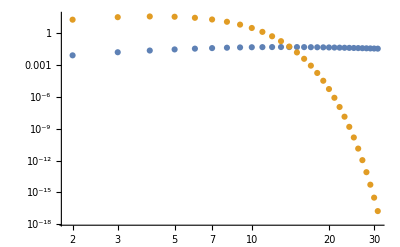

```mathematica
ListLogLogPlot[{listx, Table[4^2*10 x PDF[NormalDistribution[0,1/(√10)],x],{x,0,3,0.1}]}]
```

```mathematica
Manipulate[Plot[{t/(π^3 t^3+n^2 x^2 π t),t/(π^3 t^3+n^2 x^2 π t)Exp[(-2 π^2 (s-t)^2)/n]},{t,-5,5},PlotRange->Full],{n,1,10},{x,0,3},{s,-5,5}]
```

```mathematica
t/(π^3 t^3+n^2 x^2 π t) /. t-> s-t
```

(s-t)/(π^3 (s-t)^3+n^2 π (s-t) x^2)

```mathematica
Manipulate[Plot[{Exp[(-2 π^2 t^2)/n],Exp[(-2 π^2 t^2)/n]Abs[(s-t)/(π^3 (s-t)^3+n^2 π (s-t) x^2)]},{t,-5,5},PlotRange->{{-2,2},{0,0.2}}],{n,1,10},{x,0,3},{s,-5,5}]
```

```mathematica
z1 = (Δ + n(dx + dz) + 2π ⅈ  s)/(2 √n)
z2 = (Δ + n(-dx + dz) + 2π ⅈ s)/(2 √n)
z3 = (Δ + n(dx - dz) + 2π ⅈ s)/(2 √n)
z4 = (Δ + n(-dx - dz) + 2π ⅈ s)/(2 √n)
```

((dx+dz) n+2 ⅈ π s+Δ)/(2 √n)

((-dx+dz) n+2 ⅈ π s+Δ)/(2 √n)

((dx-dz) n+2 ⅈ π s+Δ)/(2 √n)

((-dx-dz) n+2 ⅈ π s+Δ)/(2 √n)

```mathematica
Series[1/z1-1/z2-1/z3+1/z4,{s,∞,4}]
```

(2 ⅈ dx dz n^(5/2))/(π^3 s^3)-(3 (dx dz n^(5/2) Δ))/(π^4 s^4)+O[1/s]^5

```mathematica
Series[1/z1^3-1/z2^3-1/z3^3+1/z4^3,{s,∞,6}]
```

-(12 ⅈ dx dz n^(7/2))/(π^5 s^5)+(30 dx dz n^(7/2) Δ)/(π^6 s^6)+O[1/s]^7

```mathematica
Series[1/z1^5-1/z2^5-1/z3^5+1/z4^5,{s,∞,8}]
```

(30 ⅈ dx dz n^(9/2))/(π^7 s^7)-(105 (dx dz n^(9/2) Δ))/(π^8 s^8)+O[1/s]^9

```mathematica
{30/π^6,105/π^8}//N
```

{0.0312048,0.011066}

```mathematica
InverseFourierTransform[1/s^2 n x PDF[NormalDistribution[0,1/(√n)],x]+ⅇ^(-(π s)^2/n),s,y,FourierParameters->{0, -2*Pi}]
```

((ⅇ^(-n y^2))/(√(1/n))-√2 ⅇ^(-(n x^2)/2) n^(3/2) π^2 x y Sign[y])/(√π)

```mathematica
Manipulate[Plot[{(1-Exp[-2n x y])PDF[NormalDistribution[0,1/(√n)],y-x],((ⅇ^(-n y^2))/(√(1/n))+√2 ⅇ^(-(n x^2)/2) n^(3/2) π^2 x y Sign[y])/(√π)},{x,0,3}],{n,1,10},{{y,0.5},0,3}]
```